```mathematica
SetDirectory[NotebookDirectory[]]
Get["eigenfaces-algorithm.m"]
{eigenvalues, eigenfaces}=findEigenfaces[normalizedFaces];
```

/home/nathan/QEA-Eigenfaces/Eigenfaces

```mathematica
(*clustAll gives the total tour distance between the projected images of each person. *)
clusterAll[eigenfaces_,images_,numTrainingIndividuals_]:=Module[{components},
components=Map[eigenCompress[#1,eigenfaces[[All]],All]&,images];
components=Partition[components,8];
components=MapThread[Labeled[#1,#2]&,{components,names}];
Return[Transpose[{Map[FindShortestTour,components[[1;;numTrainingIndividuals,1]]][[All,1]],components[[1;;numTrainingIndividuals,2]]}]]]
```

```mathematica
{eigenvalues43,eigenfaces43}=findEigenfaces[Map[#-Mean[#]&, Flatten/@images[[1;;344;;8]]]];
```

```mathematica
Length[eigenfaces43]
components43=Map[eigenCompress[#1,eigenfaces43[[2;;3]],All]&,images];
components43=Partition[components43,8];
components43=MapThread[Labeled[#1,#2]&,{components43,names}];
```

43

```mathematica
ListPlot[components43[[3;;13]],PlotStyle->PointSize[Large],ImageSize->Medium,PlotTheme->"Web"]
```

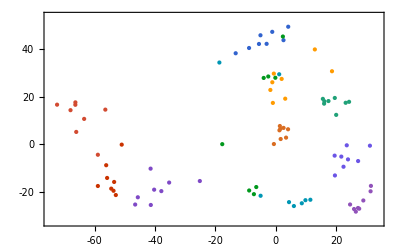

```mathematica
components3=Map[eigenCompress[#1,eigenfaces[[1;;3]],All]&,images];
components3=Partition[components3,8];
(*components3=MapThread[Labeled[#1,#2]&,{components3,names}];*)
ListPointPlot3D[components3[[All]],PlotStyle->PointSize[Large],ImageSize->Large]
```

-Graphics3D-

301

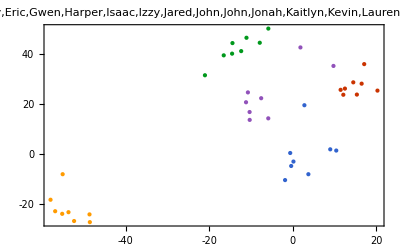

```mathematica
{eigenvalues301,eigenfaces301}=findEigenfaces[Map[#-Mean[#]&, Flatten/@images[[Complement[Range[344],Range[1,344,8]]]]]];
Length[eigenfaces301]
components301=Map[eigenCompress[#1,eigenfaces301[[2;;3]],All]&,images];
components301=Partition[components301,8];
components301=MapThread[Labeled[#1,#2]&,{components301,names}];
ListPlot[components301[[1;;5]],PlotStyle->PointSize[Large],ImageSize->Large,PlotLabel->names,PlotTheme->"Web"]
```

```mathematica
Dimensions@eigenfaces301[[1;;43,All]]
```

{43,92160}

```mathematica
Mean[clusterAll[eigenfaces43,images,43][[All,1]]]
Mean[clusterAll[eigenfaces301[[1;;43,All]],images,43][[All,1]]]
```

172.968

200.754

```mathematica
Grid[Transpose@{{"Training Size","43","301"},{"Clustering Coefficient",173,201}}]
```

Training Size | Clustering Coefficient
43 | 173
301 | 201